```mathematica
NetModel["LeNet Trained on MNIST Data","ConstructionNotebook"]
```

xfsfp_shm22FrontEndObject[LinkObject["xfsfp_shm", 3, 1]]22Untitled-2

```mathematica
uninit=NetChain[{
ConvolutionLayer[20,{5,5}],
ElementwiseLayer[Ramp],
PoolingLayer[{2,2},{2,2}],
ConvolutionLayer[50,{5,5}],
ElementwiseLayer[Ramp],
PoolingLayer[{2,2},{2,2}],
FlattenLayer[],
DotPlusLayer[500],
ElementwiseLayer[Ramp],
DotPlusLayer[512],
SoftmaxLayer[]
},
"Output"->NetDecoder[{"Class",FromCharacterCode/@Range[16^^4E00,16^^4FFF]}],
"Input"->NetEncoder[{"Image",{28,28},"Grayscale"}]
]
```

NetChain[]

```mathematica
init=NetInitialize[uninit]
```

NetChain[]

```mathematica
trainSet=Flatten[Table[ImageResize[ImageRotate[#[[1]],angle Degree,Background->White],{28,28}]->#[[2]],{angle,RandomVariate[NormalDistribution[0,8],10]}]&/@Flatten[Outer[Function[{char,font},Rasterize[Style[char,font,32]]->char],FromCharacterCode/@Range[16^^4E00,16^^4FFF],{Plain,Bold,Italic}]]];
```

```mathematica
trained=NetTrain[init,RandomSample@trainSet]
```

NetChain[]

```mathematica
testSet=Flatten[Table[ImageResize[Blur[ImageRotate[#[[1]],angle Degree,Background->White]],{28,28}]->#[[2]],{angle,RandomVariate[NormalDistribution[0,8],10]}]&/@Flatten[Outer[Function[{char,font},Rasterize[Style[char,font,32]]->char],FromCharacterCode/@Range[16^^4E00,16^^4FFF],{Plain,Bold,Italic}]]];
```

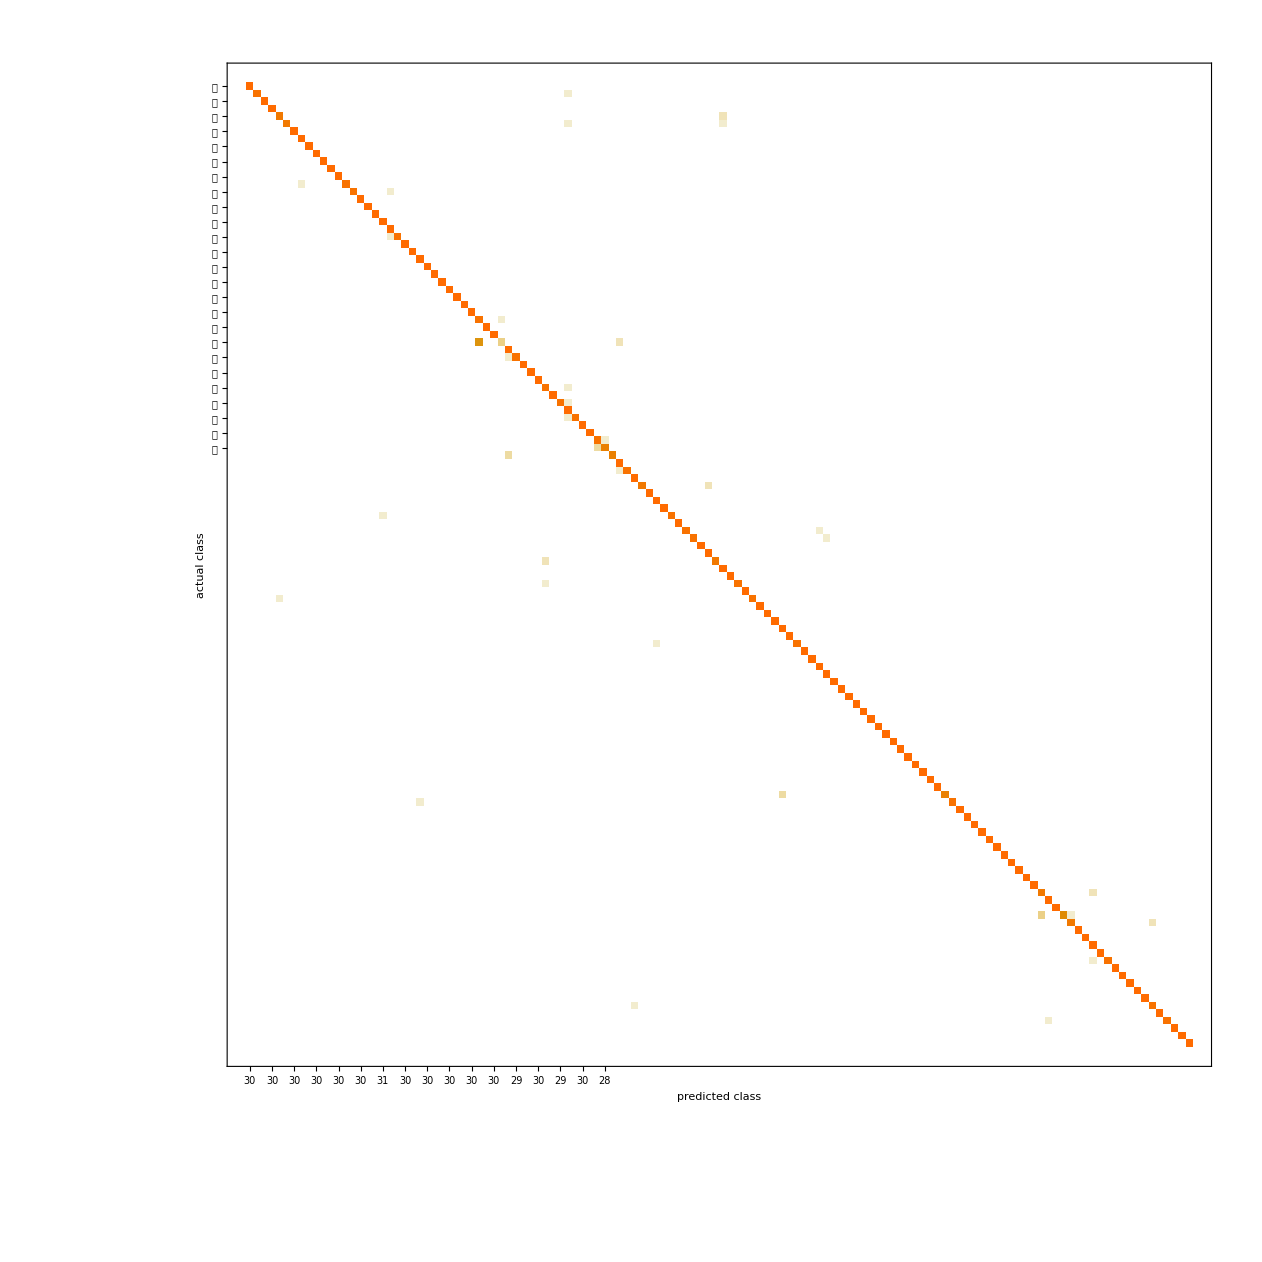

```mathematica
cm=ClassifierMeasurements[trained,testSet,"ConfusionMatrixPlot"]
```

```mathematica
ClassifierMeasurements[trained,testSet,"Accuracy"]
```

0.977083

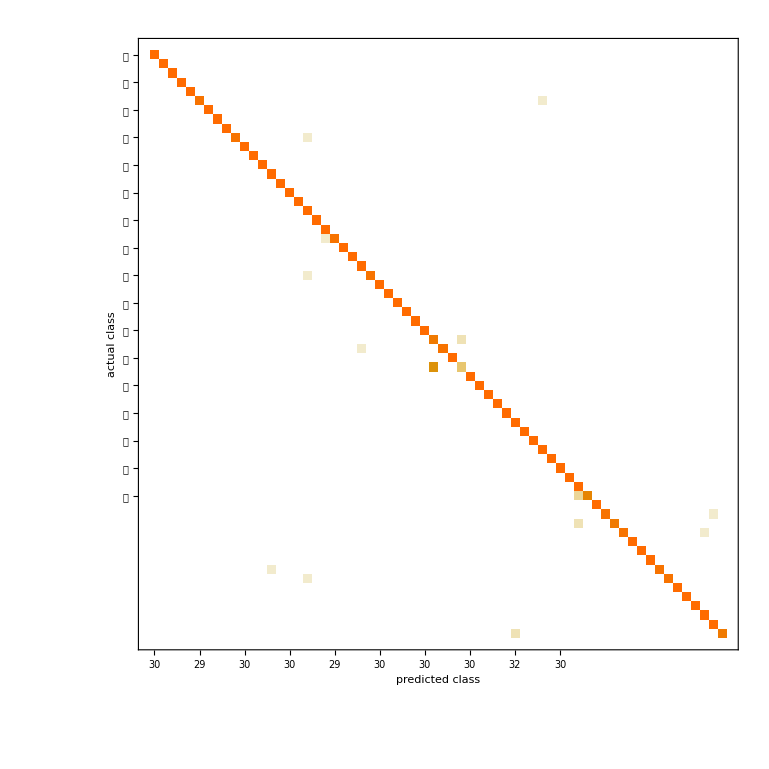

```mathematica
cm2=ClassifierMeasurements[trained,testSet,"ConfusionMatrixPlot"]
```

```mathematica
ClassifierMeasurements[trained,testSet,"Accuracy"]
```

0.978646

```mathematica
Erosion[-Graphics-,DiskMatrix[0.5]]
```

-Graphics-

```mathematica
Opening[-Graphics-,DiskMatrix[0.5]]
```

-Graphics-

```mathematica
ImageTransformation[-Graphics-,#^2&]
```

-Graphics-

```mathematica
ImageResize[Binarize[ImageCrop[-Graphics-,{300,300}]],{28,28}]
```

-Graphics-

```mathematica
trained[-Graphics-]
```

乘

```mathematica
ImageResize[Binarize[ImageCrop[-Graphics-,{300,300}]],{28,28}]
```

-Graphics-

```mathematica
trained[-Graphics-]
```

乱